```mathematica
V = {Subscript[v, 1], Subscript[v, 2], 0}
```

{v_1,v_2,0}

```mathematica
P = m V
```

{m v_1,m v_2,0}

```mathematica
R = {Subscript[r, 1],Subscript[r, 2], 0}
```

{r_1,r_2,0}

```mathematica
L = Cross[R, P]
```

{0,0,-m r_2 v_1+m r_1 v_2}

```mathematica
LRL = Cross[P, L] - k R
```

{-k r_1-m^2 r_2 v_1 v_2+m^2 r_1 v_2^2,-k r_2+m^2 r_2 v_1^2-m^2 r_1 v_1 v_2,0}

```mathematica
LRL[[2]]/LRL[[1]]   ==0
```

(-k r_2+m^2 r_2 v_1^2-m^2 r_1 v_1 v_2)/(-k r_1-m^2 r_2 v_1 v_2+m^2 r_1 v_2^2)==0

```mathematica
eq1 =Assuming[1/%[[1]][[2]] ≠ 0,MultiplySides[%,1/%[[1]][[2]]]//Simplify]
```

r_2 (-k+m^2 v_1^2)==m^2 r_1 v_1 v_2

```mathematica
eq2 = (Norm[LRL] ^2//ComplexExpand //Simplify)== a
```

-2 m^2 r_1 r_2 v_1 v_2 (-2 k+m^2 v_1^2+m^2 v_2^2)+r_1^2 (k^2+(-2 k m^2+m^4 v_1^2) v_2^2+m^4 v_2^4)+r_2^2 (k^2+m^4 v_1^4+v_1^2 (-2 k m^2+m^4 v_2^2))==a

```mathematica
Solve[{eq1, eq2}, {Subscript[v, 1],Subscript[v, 2]}]//Simplify
```

{{v_1→-√((k^2 r_2^2)/(m^2 (-√a r_1+k r_1^2+k r_2^2))),v_2→((-√a+k r_1) √((k^2 r_2^2)/(m^2 (-√a r_1+k r_1^2+k r_2^2))))/(k r_2)},{v_1→√((k^2 r_2^2)/(m^2 (-√a r_1+k r_1^2+k r_2^2))),v_2→((√a-k r_1) √((k^2 r_2^2)/(m^2 (-√a r_1+k r_1^2+k r_2^2))))/(k r_2)},{v_1→-√((k^2 r_2^2)/(m^2 (√a r_1+k r_1^2+k r_2^2))),v_2→((√a+k r_1) √((k^2 r_2^2)/(m^2 (√a r_1+k r_1^2+k r_2^2))))/(k r_2)},{v_1→√((k^2 r_2^2)/(m^2 (√a r_1+k r_1^2+k r_2^2))),v_2→-((√a+k r_1) √((k^2 r_2^2)/(m^2 (√a r_1+k r_1^2+k r_2^2))))/(k r_2)}}

```mathematica
%/.{m->1, k->1, a-> 10} //Simplify
```

{{v_1→-√(r_2^2/(-√10 r_1+r_1^2+r_2^2)),v_2→((-√10+r_1) √(r_2^2/(-√10 r_1+r_1^2+r_2^2)))/r_2},{v_1→√(r_2^2/(-√10 r_1+r_1^2+r_2^2)),v_2→((√10-r_1) √(r_2^2/(-√10 r_1+r_1^2+r_2^2)))/r_2},{v_1→-√(r_2^2/(√10 r_1+r_1^2+r_2^2)),v_2→((√10+r_1) √(r_2^2/(√10 r_1+r_1^2+r_2^2)))/r_2},{v_1→√(r_2^2/(√10 r_1+r_1^2+r_2^2)),v_2→-((√10+r_1) √(r_2^2/(√10 r_1+r_1^2+r_2^2)))/r_2}}

```mathematica
eqs =(Subscript[v, 1]^2 + Subscript[v, 2]^2  == 10)/.% //Simplify
```

{(10-2 √10 r_1+r_1^2+r_2^2)/(-√10 r_1+r_1^2+r_2^2)==10,(10-2 √10 r_1+r_1^2+r_2^2)/(-√10 r_1+r_1^2+r_2^2)==10,(10+2 √10 r_1+r_1^2+r_2^2)/(√10 r_1+r_1^2+r_2^2)==10,(10+2 √10 r_1+r_1^2+r_2^2)/(√10 r_1+r_1^2+r_2^2)==10}

```mathematica
Solve[#, Subscript[r, 2]] & /@ eqs
```

{{{r_2→-1/3 √(10+8 √10 r_1-9 r_1^2)},{r_2→1/3 √(10+8 √10 r_1-9 r_1^2)}},{{r_2→-1/3 √(10+8 √10 r_1-9 r_1^2)},{r_2→1/3 √(10+8 √10 r_1-9 r_1^2)}},{{r_2→-1/3 √(10-8 √10 r_1-9 r_1^2)},{r_2→1/3 √(10-8 √10 r_1-9 r_1^2)}},{{r_2→-1/3 √(10-8 √10 r_1-9 r_1^2)},{r_2→1/3 √(10-8 √10 r_1-9 r_1^2)}}}

```mathematica
f =Subscript[r, 2]/.# & /@ %
```

{{-1/3 √(10+8 √10 r_1-9 r_1^2),1/3 √(10+8 √10 r_1-9 r_1^2)},{-1/3 √(10+8 √10 r_1-9 r_1^2),1/3 √(10+8 √10 r_1-9 r_1^2)},{-1/3 √(10-8 √10 r_1-9 r_1^2),1/3 √(10-8 √10 r_1-9 r_1^2)},{-1/3 √(10-8 √10 r_1-9 r_1^2),1/3 √(10-8 √10 r_1-9 r_1^2)}}

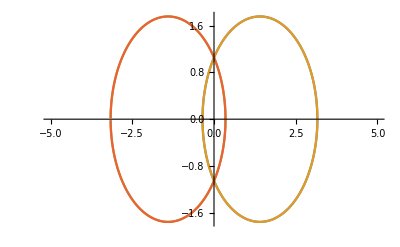

```mathematica
Plot[f, {Subscript[r, 1], -5, 5}]
```